```mathematica
f[n_,x_]:= Abs[((1/Pi)^(1/4)HermiteH[n,x])/(E^(x^2/2)Sqrt[2^n n!])]^2
```

```mathematica
Export["~/Dokumentumok/hrmmegoldas.pdf",Plot[Evaluate@
  Append[Table[f[n,x]+n+1/2,{n,0,7}],x^2/2],{x,-4,4},Filling->Table[n->n-1/2,{n,1,8}],AxesLabel->{Style["x",12,Black,FontFamily->"ComputerModern"],Style["E_n",12,Black,FontFamily->"ComputerModern"]}]]
```

~/Dokumentumok/hrmmegoldas.pdf

```mathematica
ψ[n_,l_,r_]:=√(((n-l-1)!)/((n+l)!)) ⅇ^(-r/n) ((2r)/n)^l 2/n^2 LaguerreL[n-l-1, 2l+1,(2r)/n]
```

```mathematica
Integrate[Abs[ψ[4,2,r]]^2*r^2//FullSimplify,{r,0,Infinity}]
```

1

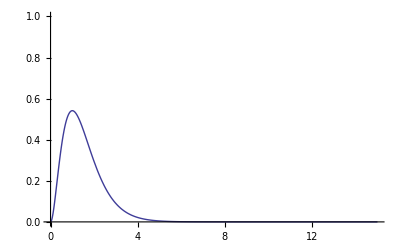

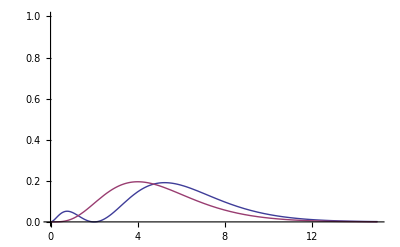

```mathematica
Plot[r^2*Abs[ψ[1,0,r]]^2,{r,0,15},PlotRange->{0,1}]
Plot[{r^2*Abs[ψ[2,0,r]]^2,r^2*Abs[ψ[2,1,r]]^2},{r,0,15},PlotRange->{0,1}]
```

```mathematica
Plot[Evaluate@
  Append[Table[Table[ψ[n,l,r]-1/n^2,{l,0,n-1}],{n,1,2}],1/r^2],{r,0,15},Filling->Table[Table[l->1/n^2,{l,0,n-1}],{n,1,2}]],AxesLabel->{Style["x",12,Black,FontFamily->"ComputerModern"],Style["E_n",12,Black,FontFamily->"ComputerModern"]}]
```

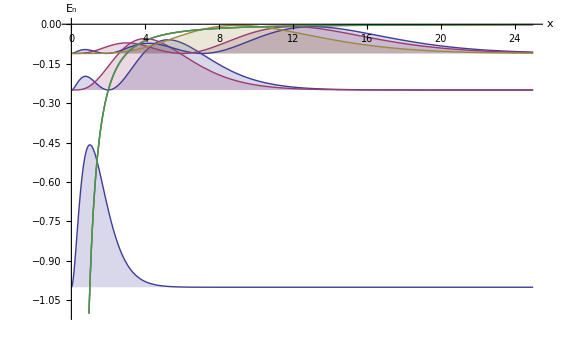

```mathematica
Show[Table[Plot[Evaluate@
  Append[Table[Abs[ψ[n,l,x]]^2*x^2-1/n^2,{l,0,n-1}],-1/x^2],{x,0,25},Filling->Table[l+1->-1/n^2,{l,0,n-1}],AxesLabel->{Style["x",12,Black,FontFamily->"ComputerModern"],Style["E_n",12,Black,FontFamily->"ComputerModern"]},PlotRange->{-1.1,0}],{n,1,3}]]
```

```mathematica
Export["~/Dokumentumok/Hp-n1.pdf",Plot[Evaluate@
  Table[Abs[ψ[1,l,x]]^2,{l,0,1-1}],{x,0,25},AxesLabel->{Style["r",12,Black,FontFamily->"ComputerModern"],Style["w_(n, l)(r)",12,Black,FontFamily->"ComputerModern"]},PlotRange->{0,1},PlotStyle->{Thick}]]
```

~/Dokumentumok/Hp-n1.pdf

```mathematica
Export["~/Dokumentumok/Hp-n2.pdf",Plot[Evaluate@
  Table[Abs[ψ[2,l,x]]^2,{l,0,2-1}],{x,0,25},AxesLabel->{Style["r",12,Black,FontFamily->"ComputerModern"],Style["w_(n, l)(r)",12,Black,FontFamily->"ComputerModern"]},PlotRange->{0,0.5},PlotStyle->{Thick}]]
```

~/Dokumentumok/Hp-n2.pdf

```mathematica
Export["~/Dokumentumok/Hp-n3.pdf",Plot[Evaluate@
  Table[Abs[ψ[3,l,x]]^2,{l,0,3-1}],{x,0,25},AxesLabel->{Style["r",12,Black,FontFamily->"ComputerModern"],Style["w_(n, l)(r)",12,Black,FontFamily->"ComputerModern"]},PlotRange->{0,0.25},PlotStyle->{Thick}]]
```

~/Dokumentumok/Hp-n3.pdf

```mathematica
Table[Table[Export["~/Dokumentumok/Y-l"<>ToString[l]<>"-m"<>ToString[m]<>".jpeg",ParametricPlot3D[
Evaluate[{Cos[p]Sin[t],Sin[p]Sin[t],Cos[t]}Abs[SphericalHarmonicY[l,m,t,p]]],
{p,-Pi,Pi},{t,0,Pi},PlotRange->{{-.6,.6},{-.6,.6},{-1,1}},
Mesh->False,PlotPoints->{45,27},MaxRecursion->ControlActive[0,2],
ViewAngle->.246,ImageSize ->{1024,1024},Axes->False,SphericalRegion->True,Boxed->False,PerformanceGoal->"Quality"]],
{m,0,l}],
{l,0,4}]
```